```mathematica
ClearAll["Global`*"]
```

```mathematica
β=0.18 / (24*60);
γ=0.03 / (24*60);
t1 = 0;
t2 =100*(24*60);
```

```mathematica
s0 = 2000;
i0 = 1000;
r0 =0;
n =s0+i0+r0;
```

```mathematica
β i0 s0 / n
```

0.0833333

```mathematica
i0/n
```

1/3

```mathematica
sol = NDSolve[{
s'[t]== -β i[t] s[t] / n,
i'[t]== β i[t] s[t] / n -γ i[t],
r'[t]== γ i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0
},{s[t],r[t],i[t]},{t,t1,t2}]
```

{{s[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t],i[t]→InterpolatingFunction[…][t]}}

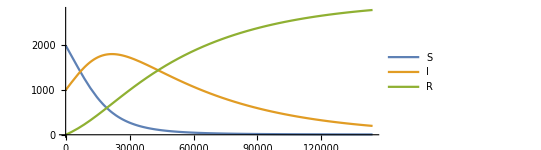

```mathematica
Plot[{
s[t]/.sol,
i[t]/.sol,
r[t]/.sol
},{t,t1,t2},PlotLegends-> {"S","I","R"},AspectRatio->3/8]
```

```mathematica
(s[t]/.sol)/.t-> 60
```

{1995.}

```mathematica
ss={2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0,2000.0};
ii={1000.0,970.0,940.9,912.673,885.29281,858.7340257000001,832.972004929,807.98284478113,783.7433594376961,760.2310586545652,737.4241268949282,715.3014030880804,693.842360995438,673.0270901655748,652.8362774606076,633.2511891367893,614.2536534626856,595.8260438588051,577.9512625430409,560.6127246667497,543.7943429267473,527.4805126389449,511.6560972597766,496.30641434198327,481.4172219117238,466.9747052543721,452.96546409674096,439.37650017383874,426.1952051686236,413.4093490135649,401.00706854315797,388.97685648686326,377.30755079225736,365.98832426848963,355.0086745404349,344.35841430422187,334.0276618750952,324.0068320188423,314.2866270582771,304.85802824652876,295.7122873991329,286.8409187771589,278.2356912138441,269.8886204774288,261.79196186310594,253.93820300721276,246.32005691699638,238.9304552094865,231.7625415532019,224.80966530660586,218.0653753474077,211.52341408698547,205.1777116643759,199.0223803144446,193.05170890501125,187.2601576378609,181.6423529087251,176.19308232146332,170.90728985181943,165.78007115626485,160.8066690215769,155.98246895092961,151.30299488240172,146.76390503592967,142.36098788485177,138.0901582483062,133.94745350085702,129.92902989583132,126.03115899895639,122.25022422898769,118.58271750211806,115.02523597705452,111.57447889774289,108.22724453081061,104.98042719488629,101.8310143790397,98.77608394766851,95.81280142923846,92.93841738636131,90.15026486477046,87.44575691882736,84.82238421126253,82.27771268492465,79.80938130437691,77.41509986524561,75.09264686928825,72.8398674632096,70.65467143931332,68.53503129613392,66.47898035724991,64.48461094653241,62.55007261813644,60.673570439592346,58.853363326404576,57.087762426612436,55.37512955381406,53.71387566719964,52.10245939718365,50.53938561526814,49.02320404681009,47.55250792540579};
rr={0.0,30.0,59.099999999999994,87.327,114.70719,141.2659743,167.02799507100002,192.01715521887002,216.25664056230391,239.7689413454348,262.57587310507176,284.6985969119196,306.157639004562,326.97290983442514,347.1637225393924,366.7488108632106,385.7463465373143,404.1739561411949,422.04873745695903,439.3872753332503,456.2056570732528,472.5194873610552,488.34390274022354,503.69358565801684,518.5827780882763,533.025294745628,547.0345359032592,560.6234998261615,573.8047948313766,586.5906509864353,598.9929314568423,611.023143513137,622.6924492077429,634.0116757315106,644.9913254595654,655.6415856957784,665.972338124905,675.9931679811579,685.7133729417232,695.1419717534715,704.2877126008673,713.1590812228412,721.764308786156,730.1113795225713,738.2080381368942,746.0617969927873,753.6799430830036,761.0695447905135,768.2374584467981,775.1903346933941,781.9346246525923,788.4765859130146,794.8222883356241,800.9776196855554,806.9482910949887,812.739842362139,818.3576470912749,823.8069176785366,829.0927101481805,834.219928843735,839.193330978423,844.0175310490703,848.6970051175981,853.2360949640702,857.639012115148,861.9098417516935,866.0525464991427,870.0709701041685,873.9688410010434,877.7497757710121,881.4172824978817,884.9747640229452,888.4255211022569,891.7727554691892,895.0195728051135,898.1689856209601,901.2239160523313,904.1871985707614,907.0615826136386,909.8497351352295,912.5542430811726,915.1776157887374,917.7222873150753,920.190618695623,922.5849001347543,924.9073531307117,927.1601325367903,929.3453285606867,931.464968703866,933.52101964275,935.5153890534675,937.4499273818635,939.3264295604076,941.1466366735954,942.9122375733875,944.6248704461859,946.2861243328003,947.8975406028163,949.4606143847318,950.9767959531898,952.4474920745942};
ts={0.0,1.0,2.0,3.0,4.0,5.0,6.0,7.0,8.0,9.0,10.0,11.0,12.0,13.0,14.0,15.0,16.0,17.0,18.0,19.0,20.0,21.0,22.0,23.0,24.0,25.0,26.0,27.0,28.0,29.0,30.0,31.0,32.0,33.0,34.0,35.0,36.0,37.0,38.0,39.0,40.0,41.0,42.0,43.0,44.0,45.0,46.0,47.0,48.0,49.0,50.0,51.0,52.0,53.0,54.0,55.0,56.0,57.0,58.0,59.0,60.0,61.0,62.0,63.0,64.0,65.0,66.0,67.0,68.0,69.0,70.0,71.0,72.0,73.0,74.0,75.0,76.0,77.0,78.0,79.0,80.0,81.0,82.0,83.0,84.0,85.0,86.0,87.0,88.0,89.0,90.0,91.0,92.0,93.0,94.0,95.0,96.0,97.0,98.0,99.0,100.0};
```

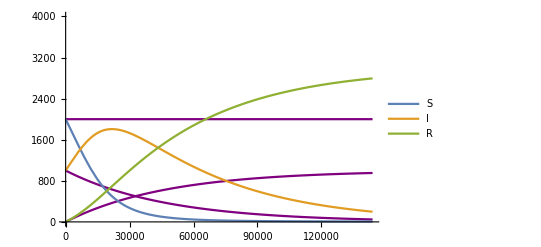

```mathematica
Show[{
ListPlot[ {ts(24*60), ss}//Transpose,Joined->True, PlotStyle->Purple],
ListPlot[ {ts(24*60), ii}//Transpose,Joined->True, PlotStyle->Purple],
ListPlot[ {ts(24*60), rr}//Transpose,Joined->True, PlotStyle->Purple],
Plot[{
s[t]/.sol,
i[t]/.sol,
r[t]/.sol
},{t,t1,t2},PlotLegends-> {"S","I","R"},AspectRatio->3/8]
}]
```